Mathematica code presented here is taken from Ravaud and Lemarquand [1].

The x_1,x_2, y_1,y_2,z_1,z_2 subscripted dimensions of a Parallelpiped (see image below taken from [1]).

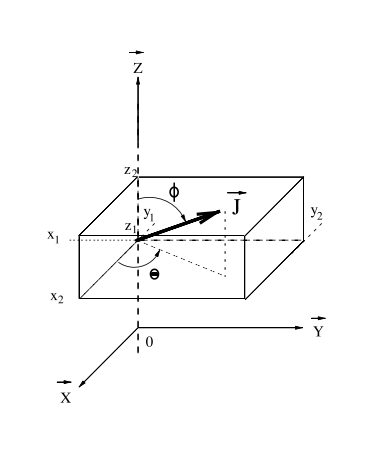

```mathematica
X[l_]:=Subscript[x,ToExpression[l]];
Y[l_]:=Subscript[y,ToExpression[l]];
Z[l_]:=Subscript[z,ToExpression[l]];
```

Distance between some corner of the parallelpiped and an arbitrary point in space.

```mathematica
ξ[i_,j_,k_]:=√((x-X[i])^2+(y-Y[j])^2+(z-Z[k])^2);
```

Boundary integrals for each surface (eqn. 6 in [1]).

```mathematica
Φ1[i_,j_,k_]:=Z[k]+(x-X[i])ArcTan[(z-Z[k])/(x-X[i])]+(y-Y[j])Log[z-Z[k]+ξ[i,j,k]]-(x-X[i])ArcTan[((y-Y[j])(z-Z[k]))/((x-X[i])ξ[i,j,k])]+(z-Z[k])Log[y-Y[j]+ξ[i,j,k]];
Φ2[i_,j_,k_]:=Z[k]+(y-Y[j])ArcTan[(z-Z[k])/(y-Y[j])]+(x-X[i])Log[z-Z[k]+ξ[i,j,k]]-(y-Y[j])ArcTan[((x-X[i])(z-Z[k]))/((y-Y[j])ξ[i,j,k])]+(z-Z[k])Log[x-X[i]+ξ[i,j,k]];
Φ3[i_,j_,k_]:=Y[j]+(z-Z[k])ArcTan[(y-Y[j])/(z-Z[k])]+(x-X[i])Log[y-Y[j]+ξ[i,j,k]]-(z-Z[k])ArcTan[((x-X[i])(y-Y[j]))/((z-Z[k])ξ[i,j,k])]+(y-Y[j])Log[x-X[i]+ξ[i,j,k]]
```

Expression for the scalar potential (eqn. 5 in [1]) with
J - Polarization magnitude
θ - Azimuthal angle of uniform polarization (see image above), 0 ≤ θ < 2π
ϕ - Polar angle of uniform polarization (see image above), 0 ≤ ϕ ≤ π
x1 ... z2 - parallelpiped dimensions (see image above)

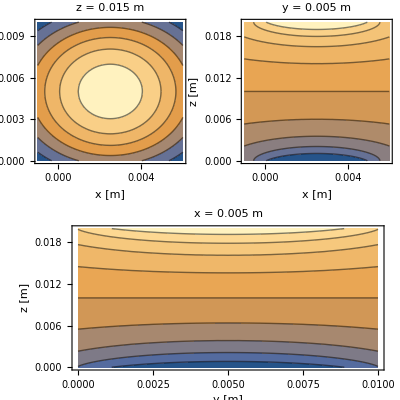

-Graphics3D-

```mathematica
MagneticPotential[J_,μ_,θ_,ϕ_,x1_,x2_,y1_,y2_,z1_,z2_]:=Module[{expr},
expr=J/(4π μ)*Sum[(-1)^(i+j+k)(Sin[ϕ]Cos[θ]Φ1[i,j,k]+Sin[ϕ]Sin[θ]Φ2[i,j,k]+Cos[ϕ]Φ3[i,j,k]),{i,1,2},{j,1,2},{k,1,2}]/.{Subscript[x, 1]->x1,Subscript[x, 2]->x2,Subscript[y, 1]->y1,Subscript[y, 2]->y2,Subscript[z, 1]->z1,Subscript[z, 2]->z2};
expr
]

(* Unit: meters *)
Lx=0.005; (* 5mm *)
Ly=0.01; (* 10mm *)
Lz=0.02; (* 20mm *)
μ0=4π*10^-7;

Φ=MagneticPotential[1,μ0,0,0,0,Lx,0,Ly,0,Lz];
H={-D[Φ,x],-D[Φ,y],-D[Φ,z]};

GraphicsGrid[{
{ContourPlot[Φ/.{x->u,y->v,z->15/1000},{u,-1/1000,6/1000},{v,0,10/1000},Exclusions->None,AspectRatio->1,FrameLabel->{"x [m]","y [m]"},PlotLabel->"z = 0.015 m"],
ContourPlot[Φ/.{x->u,y->5/1000,z->v},{u,-1/1000,6/1000},{v,0,20/1000},AspectRatio->1,
FrameLabel->{"x [m]","z [m]"},PlotLabel->"y = 0.005 m"]},
{ContourPlot[Φ/.{x->5/1000,y->u,z->v},{u,0,10/1000},{v,0,20/1000},AspectRatio->1,
FrameLabel->{"y [m]","z [m]"},PlotLabel->"x = 0.005 m"],SpanFromLeft}
},PlotLabel->"Contour plots reproduced from [1] (note how the second plot is different, this ispossibly a mistake in the paper)."]

VectorPlot3D[H/.{x->u,y->v,z->w},{u,-1/1000,6/1000},{v,0,10/1000},{w,0,20/1000},VectorStyle->"Arrow3D",BoxRatios->{1, 1, 1},AxesLabel->{x,y,z}]
```

Here we check to see whether the demagnetizing field in the centre of a cube is -1/3 the magnetization.

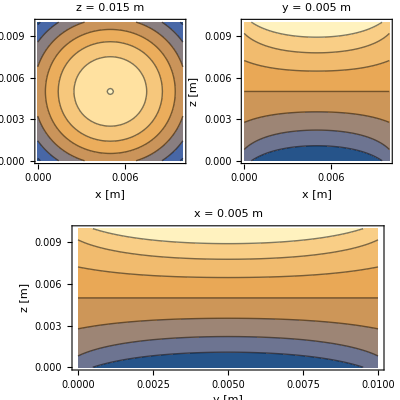

-Graphics3D-

{1.10436×10^-17,8.83487×10^-18,-0.333333}

```mathematica
(* Unit: meters *)
Lx=0.01; (* 5mm *)
Ly=0.01; (* 10mm *)
Lz=0.01; (* 20mm *)
μ0=4π*10^-7;

Φ=MagneticPotential[1,1,0,0,0,Lx,0,Ly,0,Lz];
H={-D[Φ,x],-D[Φ,y],-D[Φ,z]};

GraphicsGrid[{
{ContourPlot[Φ/.{x->u,y->v,z->15/1000},{u,0,10/1000},{v,0,10/1000},Exclusions->None,AspectRatio->1,FrameLabel->{"x [m]","y [m]"},PlotLabel->"z = 0.015 m"],
ContourPlot[Φ/.{x->u,y->5/1000,z->v},{u,0,10/1000},{v,0,10/1000},AspectRatio->1,
FrameLabel->{"x [m]","z [m]"},PlotLabel->"y = 0.005 m"]},
{ContourPlot[Φ/.{x->5/1000,y->u,z->v},{u,0,10/1000},{v,0,10/1000},AspectRatio->1,
FrameLabel->{"y [m]","z [m]"},PlotLabel->"x = 0.005 m"],SpanFromLeft}
},PlotLabel->"Contour plots reproduced from [1] (note how the second plot is different, this ispossibly a mistake in the paper)."]

VectorPlot3D[H/.{x->u,y->v,z->w},{u,0,10/1000},{v,0,10/1000},{w,0,10/1000},VectorStyle->"Arrow3D",BoxRatios->{1, 1, 1},AxesLabel->{x,y,z}]

Print[H/.{x->0.01/2,y->0.01/2,z->0.01/2}]
```

## Bibliography

[1] Romain Ravaud and Guy Lemarquand. Magnetic Field Produced by a Parallelepipedic Magnet of Various and Uniform Polarization. Progress In Electromagnetics Research, 98:207–219, 2009.